# Singular Spectrum Analysis

```mathematica
len=200
```

200

```mathematica
a1=Table[N[2*i/len],{i,len}];
```

```mathematica
Export["~/ssa_20211008/graph1.csv",a1,"CSV"]
```

~/ssa_20211008/graph1.csv

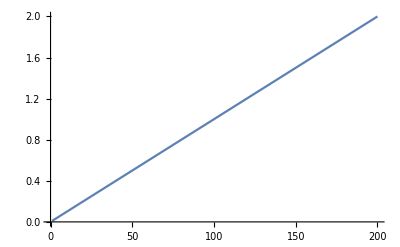

```mathematica
ListPlot[a1,Joined->True]
```

```mathematica
a2=Table[0.5*Sin[2Pi(20*i/len)],{i,len}];
```

```mathematica
Export["~/ssa_20211008/graph2.csv",a2,"CSV"]
```

~/ssa_20211008/graph2.csv

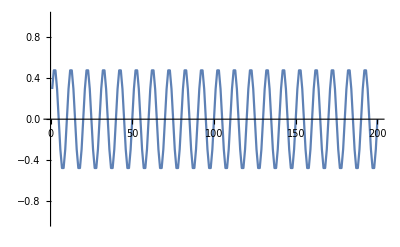

```mathematica
ListPlot[a2,Joined->True,PlotRange->{-1,1}]
```

```mathematica
c=a1+a2;
```

```mathematica
Export["~/ssa_20211008/graph3.csv",c,"CSV"]
```

~/ssa_20211008/graph3.csv

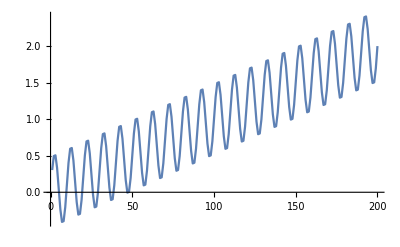

```mathematica
ListPlot[c,Joined->True]
```

```mathematica
c[[1]]
```

0.303893

```mathematica
Length[c]
```

200

200

0

```mathematica
Dimensions[c]
```

{200}

{200}

```mathematica
m=Length[c]
```

200

```mathematica
n=Floor[m/2]
```

100

```mathematica
m-n+1
```

101

```mathematica
%+n
```

201

```mathematica
x=N[Table[c[[i+j-1]],{i,m-n+1},{j,n}]];
```

```mathematica
Dimensions[x]
```

{101,100}

```mathematica
?SingularValueDecomposition
```

```mathematica
uu=SingularValueDecomposition[x];
```

```mathematica
Dimensions[uu]
```

{3}

```mathematica
u=uu[[1]];
```

```mathematica
w=uu[[2]];
```

```mathematica
v=uu[[3]];
```

```mathematica
Dimensions[u]
```

{101,101}

```mathematica
Dimensions[w]
```

{101,100}

```mathematica
Dimensions[v]
```

{100,100}

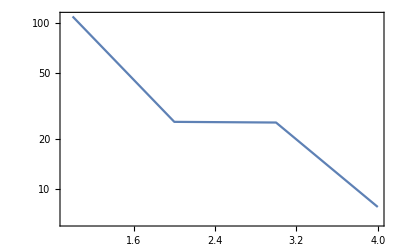

```mathematica
ListLogPlot[Table[w[[i,i]],{i,n}],Joined->True,PlotRange->All,Axes->False,Frame->True]
```

```mathematica
sn[xx_]:=Module[{i,j,k,n,n1,x,sum},x={};
{n1,n}=Dimensions[xx];
j=0;sum=0;
Do[Do[If[k≤n,sum=sum+xx[[i-k+1,k]];j=j+1],{k,i}];
x=Append[x,sum/j];sum=0;j=0,{i,n1}];
j=0;sum=0;
     Do[Do[If[k≤n1,sum=sum+xx[[n1-k+1,k+i-1]];j=j+1],{k,n-i+1}];
x=Append[x,sum/j];sum=0;j=0,{i,2,n}];
Return[x]]
```

## 0

## trend and steady

```mathematica
xx=Sum[w[[i,i]]Outer[Times,Transpose[u][[i]],Transpose[v][[i]]],{i,1}];
```

```mathematica
y1=sn[xx];
```

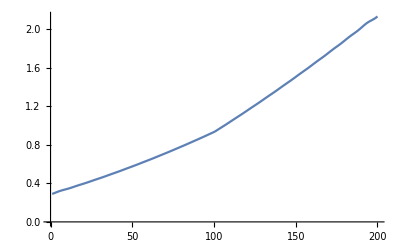

```mathematica
ListPlot[y1,Joined->True,PlotRange->All]
```

```mathematica
xx=Sum[w[[i,i]]Outer[Times,Transpose[u][[i]],Transpose[v][[i]]],{i,3}];
```

```mathematica
y1=sn[xx];
```

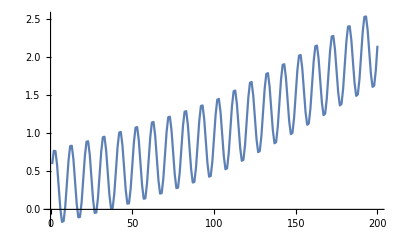

```mathematica
ListPlot[y1,Joined->True]
```

```mathematica
xx=Sum[w[[i,i]]Outer[Times,Transpose[u][[i]],Transpose[v][[i]]],{i,2,40}];
```

```mathematica
y1=sn[xx];
```

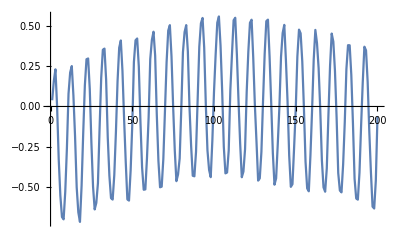

```mathematica
ListPlot[y1,Joined->True]
```

nl = {{1, 2}, {1, 3}, {1, 4}, {1, 5}, {2, 3}, {2, 4}, {2, 5}, {3, 4}, {3, 5}, {4, 5}}

{{1, 2}, {1, 3}, {1, 4}, {1, 5}, {2, 3}, {2, 4}, {2, 5}, {3, 4}, {3, 5}, {4, 5}}

Length[nl]

10

e = Table[Table[y1[[nl[[i, 1]]]].RotateLeft[y1[[nl[[i, 2]]]], k], {k, 0, Length[y1[[1]]]}]/Length[y1[[1]]], {i, 10}];

mx = Table[Max[e[[i]]], {i, Length[e]}]

{0.0034118, 0.00169974, 0.0040271, 0.00480403, 0.00241246, 0.00589803, 0.0076644, 0.00332483, 0.0041586, 0.00897104}

mn = Table[Min[e[[i]]], {i, Length[e]}]

{-0.00341771, -0.00201093, -0.00489775, -0.00717114, -0.00222704, -0.00447804, -0.00881531, -0.00401223, -0.00477609, -0.0100329}

Table[ListPlot[e[[k]], Joined -> True], {k, 10}]

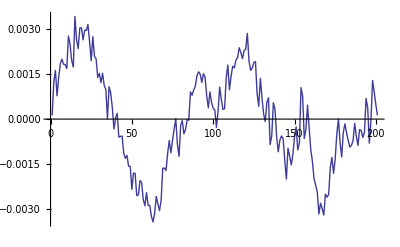
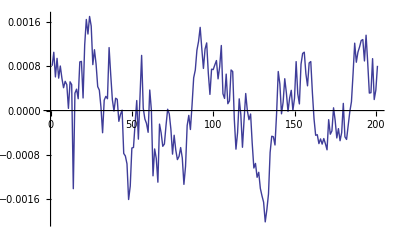
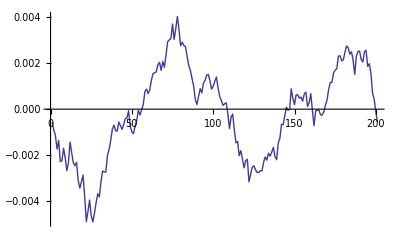
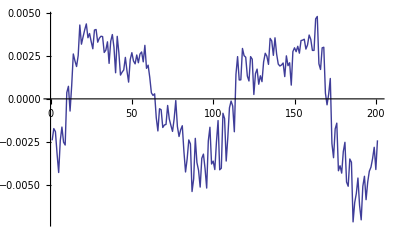
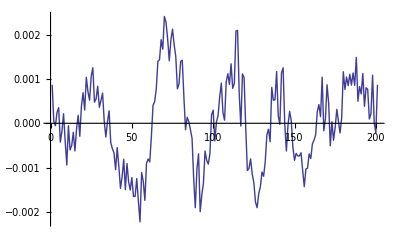
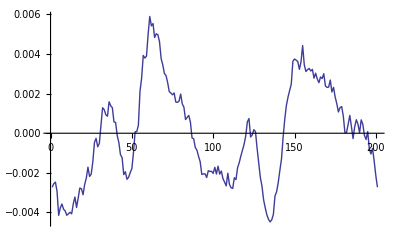
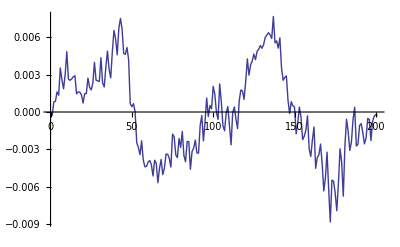
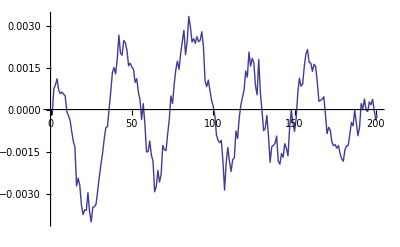

z = Table[0, {10}]

{0, 0, 0, 0, 0, 0, 0, 0, 0, 0}

Do[Do[If[e[[k, i]] == mx[[k]], z[[k]] = i], {i, Length[e[[1]]]}], {k, 10}]

z

{15, 24, 78, 164, 70, 61, 137, 85, 17, 174}